```mathematica
SetDirectory["C:\\Users\\mi\\CLionProjects\\bifurk\\results"]
```

C:\Users\mi\CLionProjects\bifurk\results

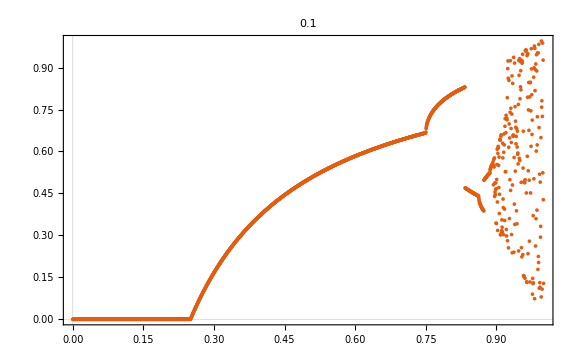
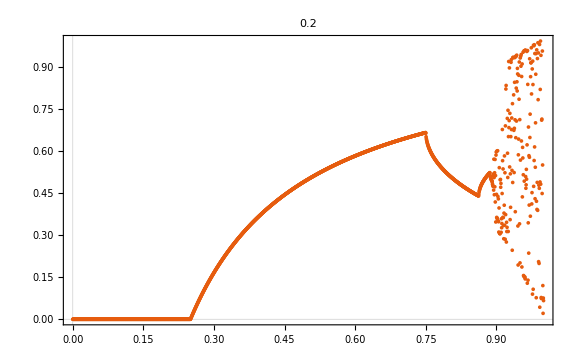
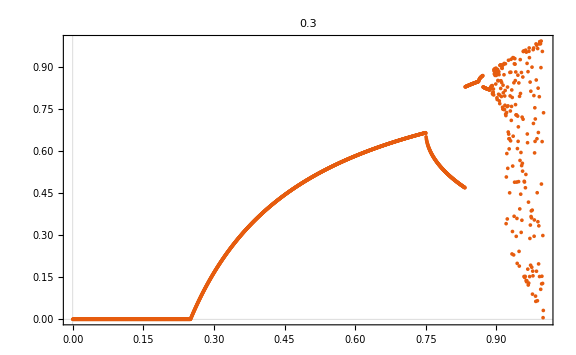
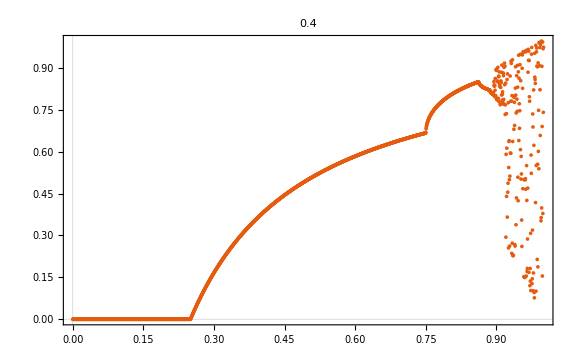

```mathematica
names = FileNames[];
allData = Table[{name, Import[name,"Table"]},{name, names}];
Table[ListPlot[subData[[2]],ImageSize->Large,PlotTheme->"Scientific",PlotLabel->ToExpression[subData[[1]]]0.1],{subData,allData}]
```

```mathematica
ToExpression@allData[[1,1]]
```

1

```mathematica
ListPlot[Table[subData[[2]],{subData,allData}],ImageSize->Large,PlotTheme->"Scientific"]
```

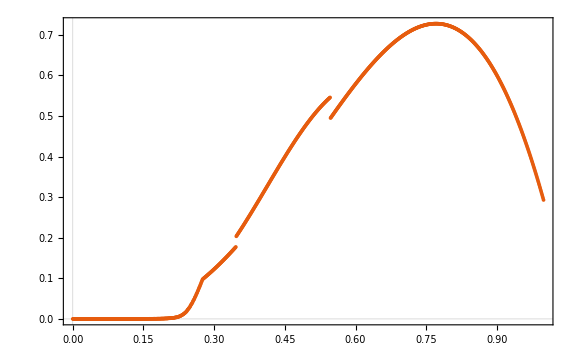

```mathematica
data = Import["data.txt","Table"];
ListPlot[data,ImageSize->Large,PlotTheme->"Scientific"]
```

```mathematica
allData = {}
```

{}

```mathematica
allData = allData~Join~{0.
```

{{1,1},{1,1}}